```mathematica
Z=28;A=56;
x=1.009^3(2ρ6*Z)/(3β*A);
Subscript[D, 1][z_]:=1+0.4228z+0.1014 z^2+0.00624 z^3;
Subscript[D, 2][z_]:=1+0.4535 z^(2/3)+0.03008z-0.05043 z^2+0.004314 z^3;
```

```mathematica
Q[B13_,ρ6_,T_]:=9.04*10^14 B13^2(T/10^9)^2 Exp[-(1.34*10^9 B13)/(2(1+(1.009^3(2ρ6*Z*4.41)/(3B13*A))^2)^0.5 T)]Subscript[D, 1][(1.34*10^9 B13)/((1+(1.009^3(2ρ6*Z*4.41)/(3B13*A))^2)^0.5 T)]Subscript[D, 2][(1.34*10^9 B13)/((1+(1.009^3(2ρ6*Z*4.41)/(3B13*A))^2)^0.5 T)];
```

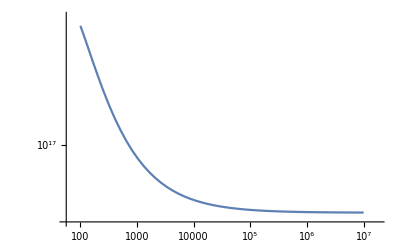

```mathematica
LogLogPlot[Q[10,ρ6,10^9],{ρ6,100,10^7}]
```

```mathematica
QB[B13_,ρ6_,T_]:=9.04*10^14 B13^2(T/10^9)^2(1-((1.34*10^9 B13)/((1+(1.009^3(2ρ6*Z*4.41)/(3B13*A))^2)^0.5 T))^(2/3));
```

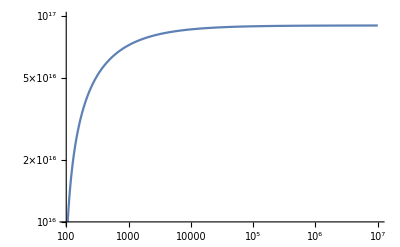

```mathematica
LogLogPlot[QB[10,ρ6,10^9],{ρ6,100,10^7},PlotRange->{{100,10^7},{10^16,10^17}}]
```

```mathematica
RR00[x_]:=1+12.306728780393993/x^(1/2)+159.28494555577515/x^(3/2)+866.7067019290372/x^(5/2)+4511.652667090261/x^(7/2)+10960.54437176578/x^(9/2)+20170.404437273137/x^(11/2)+16575.589106915428/x^(13/2)+2991.9346396672163/x^(15/2);
```

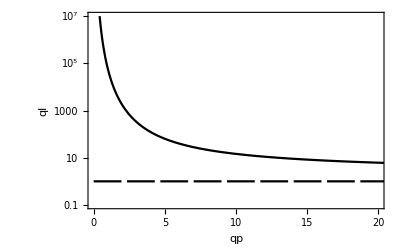

```mathematica
LogPlot[{RR00[x] ,1},{x,0,40},Frame->True,PlotRange->{{0,20},{0.1,10^7}},PlotStyle->{Black,{Black,Dashing[{0.05,0.01}]},{Black,Dashing[{0.005,0.001}]}},RotateLabel->False,FrameLabel->{"qp","ql"}]
```